## TemplateRandomOvalish-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 15:17:56
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

There are 500 cells in the tissue.

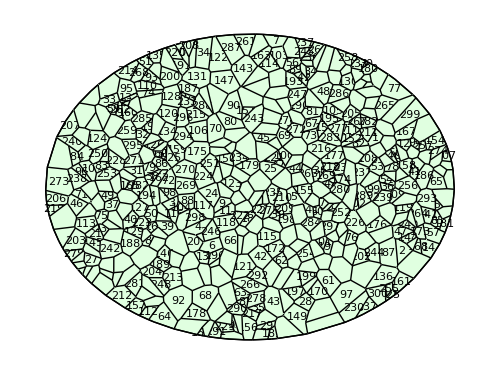

```mathematica
q=TemplateRandomOvalish[500, {100, 75}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, ImageSize-> 500]
```